```mathematica
Text[This is for one of the loop];

B=(μ* I1)/(4 π)*(-(R^2-R*x*Cos[θ] +d/2*Sin[θ])/((√(x^2-2x*R*Cos[θ]+R^2+d^2/4+d*R*Sin[θ]))^3)+(R^2-R*x*Cos[θ]- R*d/2*Sin[θ])/((√(x^2-2x*R*Cos[θ]+R^2+d^2/4-d*R*Sin[θ]))^3));
```

```mathematica
μ=10^-7;I1=1;R=0.01;d=0.1;
```

```mathematica
Re[NIntegrate[Table[(B),{x,0,4,0.1}],{θ,0,2 π},MaxRecursion->7,AccuracyGoal->9,Method->{Automatic,"SymbolicProcessing"->0}]]
```

{6.41292×10^-6,1.07871×10^-7,5.00706×10^-9,7.14765×10^-10,1.74584×10^-10,5.79837×10^-11,2.34742×10^-11,1.0909×10^-11,5.61152×10^-12,3.12017×10^-12,1.84504×10^-12,1.14683×10^-12,7.42854×10^-13,4.98153×10^-13,3.44076×10^-13,2.43787×10^-13,1.76607×10^-13,1.30461×10^-13,9.80532×10^-14,7.4841×10^-14,5.792×10^-14,4.53882×10^-14,3.59732×10^-14,2.88071×10^-14,2.32875×10^-14,1.89896×10^-14,1.56092×10^-14,1.29258×10^-14,1.07773×10^-14,9.04344×10^-15,7.63375×10^-15,6.47969×10^-15,5.52878×10^-15,4.74051×10^-15,4.08333×10^-15,3.53249×10^-15,3.06846×10^-15,2.67569×10^-15,2.34173×10^-15,2.05656×10^-15,1.81206×10^-15}

```mathematica
Fit[%,{1,x},x]
```

-3.17936×10^-7+2.27203×10^-8 x

```mathematica
Fit[%,{1,x},x]
```

6.36317×10^-7-2.27203×10^-8 x

```mathematica
Export["1.dat",%];
```

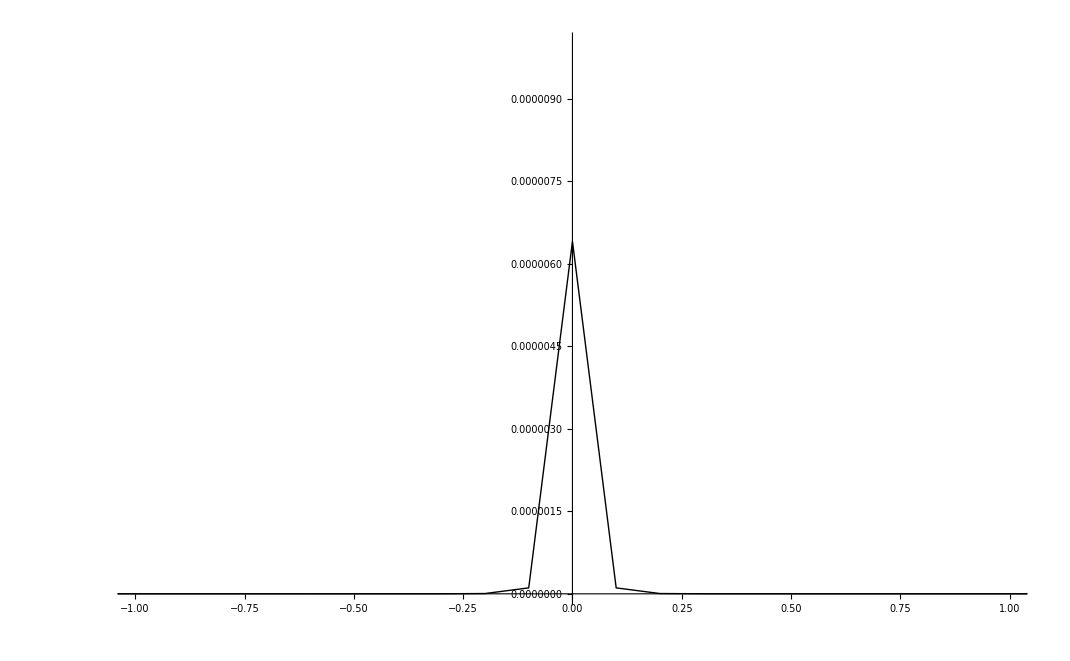

```mathematica
data=Table[{X},{X,-4,4,0.1}];
Export["2.dat",%];
finaldata=Import["3.xls"];
 
ListPlot[finaldata,Joined->True,PlotStyle->{Thick,Black},PlotRange->{{-1,1},{0,10^-5}}]
```

```mathematica
Fit[finaldata,{1,x},x]




finaldata
```

Fit::fitd: First argument {{{-4., 1.81×10^-15}, {-3.9, 2.06×10^-15}, {-3.8, 2.34×10^-15}, {-3.7, 2.68×10^-15}, {-3.6, 3.07×10^-15}, {-3.5, 3.53×10^-15}, {-3.4, 4.08×10^-15}, {-3.3, 4.74×10^-15}, {-3.2, 5.53×10^-15}, {-3.1, 6.48×10^-15}, « 71 »}} in Fit is not a list or a rectangular array.

Fit[{{{-4.,1.81×10^-15},{-3.9,2.06×10^-15},{-3.8,2.34×10^-15},{-3.7,2.68×10^-15},{-3.6,3.07×10^-15},{-3.5,3.53×10^-15},{-3.4,4.08×10^-15},{-3.3,4.74×10^-15},{-3.2,5.53×10^-15},{-3.1,6.48×10^-15},{-3.,7.63×10^-15},{-2.9,9.04×10^-15},{-2.8,1.08×10^-14},{-2.7,1.29×10^-14},{-2.6,1.56×10^-14},{-2.5,1.9×10^-14},{-2.4,2.33×10^-14},{-2.3,2.88×10^-14},{-2.2,3.6×10^-14},{-2.1,4.54×10^-14},{-2.,5.79×10^-14},{-1.9,7.48×10^-14},{-1.8,9.81×10^-14},{-1.7,1.3×10^-13},{-1.6,1.77×10^-13},{-1.5,2.44×10^-13},{-1.4,3.44×10^-13},{-1.3,4.98×10^-13},{-1.2,7.43×10^-13},{-1.1,1.15×10^-12},{-1.,1.85×10^-12},{-0.9,3.12×10^-12},{-0.8,5.61×10^-12},{-0.7,1.09×10^-11},{-0.6,2.35×10^-11},{-0.5,5.8×10^-11},{-0.4,1.75×10^-10},{-0.3,7.15×10^-10},{-0.2,5.01×10^-9},{-0.1,1.08×10^-7},{2.22045×10^-16,6.41×10^-6},{0.1,1.08×10^-7},{0.2,5.01×10^-9},{0.3,7.15×10^-10},{0.4,1.75×10^-10},{0.5,5.8×10^-11},{0.6,2.35×10^-11},{0.7,1.09×10^-11},{0.8,5.61×10^-12},{0.9,3.12×10^-12},{1.,1.85×10^-12},{1.1,1.15×10^-12},{1.2,7.43×10^-13},{1.3,4.98×10^-13},{1.4,3.44×10^-13},{1.5,2.44×10^-13},{1.6,1.77×10^-13},{1.7,1.3×10^-13},{1.8,9.81×10^-14},{1.9,7.48×10^-14},{2.,5.79×10^-14},{2.1,4.54×10^-14},{2.2,3.6×10^-14},{2.3,2.88×10^-14},{2.4,2.33×10^-14},{2.5,1.9×10^-14},{2.6,1.56×10^-14},{2.7,1.29×10^-14},{2.8,1.08×10^-14},{2.9,9.04×10^-15},{3.,7.63×10^-15},{3.1,6.48×10^-15},{3.2,5.53×10^-15},{3.3,4.74×10^-15},{3.4,4.08×10^-15},{3.5,3.53×10^-15},{3.6,3.07×10^-15},{3.7,2.68×10^-15},{3.8,2.34×10^-15},{3.9,2.06×10^-15},{4.,1.81×10^-15}}},{1,x},x]

{{{-4.,1.81×10^-15},{-3.9,2.06×10^-15},{-3.8,2.34×10^-15},{-3.7,2.68×10^-15},{-3.6,3.07×10^-15},{-3.5,3.53×10^-15},{-3.4,4.08×10^-15},{-3.3,4.74×10^-15},{-3.2,5.53×10^-15},{-3.1,6.48×10^-15},{-3.,7.63×10^-15},{-2.9,9.04×10^-15},{-2.8,1.08×10^-14},{-2.7,1.29×10^-14},{-2.6,1.56×10^-14},{-2.5,1.9×10^-14},{-2.4,2.33×10^-14},{-2.3,2.88×10^-14},{-2.2,3.6×10^-14},{-2.1,4.54×10^-14},{-2.,5.79×10^-14},{-1.9,7.48×10^-14},{-1.8,9.81×10^-14},{-1.7,1.3×10^-13},{-1.6,1.77×10^-13},{-1.5,2.44×10^-13},{-1.4,3.44×10^-13},{-1.3,4.98×10^-13},{-1.2,7.43×10^-13},{-1.1,1.15×10^-12},{-1.,1.85×10^-12},{-0.9,3.12×10^-12},{-0.8,5.61×10^-12},{-0.7,1.09×10^-11},{-0.6,2.35×10^-11},{-0.5,5.8×10^-11},{-0.4,1.75×10^-10},{-0.3,7.15×10^-10},{-0.2,5.01×10^-9},{-0.1,1.08×10^-7},{2.22045×10^-16,6.41×10^-6},{0.1,1.08×10^-7},{0.2,5.01×10^-9},{0.3,7.15×10^-10},{0.4,1.75×10^-10},{0.5,5.8×10^-11},{0.6,2.35×10^-11},{0.7,1.09×10^-11},{0.8,5.61×10^-12},{0.9,3.12×10^-12},{1.,1.85×10^-12},{1.1,1.15×10^-12},{1.2,7.43×10^-13},{1.3,4.98×10^-13},{1.4,3.44×10^-13},{1.5,2.44×10^-13},{1.6,1.77×10^-13},{1.7,1.3×10^-13},{1.8,9.81×10^-14},{1.9,7.48×10^-14},{2.,5.79×10^-14},{2.1,4.54×10^-14},{2.2,3.6×10^-14},{2.3,2.88×10^-14},{2.4,2.33×10^-14},{2.5,1.9×10^-14},{2.6,1.56×10^-14},{2.7,1.29×10^-14},{2.8,1.08×10^-14},{2.9,9.04×10^-15},{3.,7.63×10^-15},{3.1,6.48×10^-15},{3.2,5.53×10^-15},{3.3,4.74×10^-15},{3.4,4.08×10^-15},{3.5,3.53×10^-15},{3.6,3.07×10^-15},{3.7,2.68×10^-15},{3.8,2.34×10^-15},{3.9,2.06×10^-15},{4.,1.81×10^-15}}}